```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak-theory

```mathematica
NL=256;(*格子数*)
L=10^-12;(*物理的ボックスサイズ in Mpc*)
npeak=16;(*パワースペクトルのピーク波数*)
kpeak=(2π npeak)/NL
```

π/8

```mathematica
(*乱数シード, Subscript[μ̂, 2], Subscript[k̂, 3], k_*Subscript[r, m], Subscript[ζ, m], Subscript[C, m] (あるいは Subscript[C̄, m]), ln W が出力されている想定. 自分のデータに応じて適宜修正*)
SamplingData=Import["data/LN_muk_0,01_256_16_16_GB.csv"];
Ntot=Length[SamplingData](*サンプリング数*)
```

2000

```mathematica
Cth=0.533;(*平均コンパクションを使ってるなら 0.4*)
```

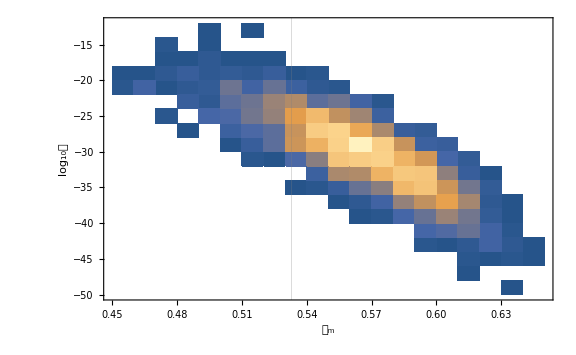

```mathematica
DensityHistogram[Map[{#[[6]],Log10[Exp[#[[7]]]]}&,SamplingData],FrameLabel->{Subscript[𝒞, "m"],"log_10𝒲"},GridLines->{{Cth},None}]
```

```mathematica
MPBH[xm_,zetam_,Cm_]=xm^2 E^(2zetam)(Cm-Cth)^γ/.{γ->0.36};(*Subscript[M, PBH]/M_(k_*)*)
```

```mathematica
Mks=(NL/L kpeak/(1.56 10^13))^-2(*M_(k_*) in 10^20 g*)
```

0.0240796

```mathematica
MPBHList=Map[{#[[3]],MPBH[#[[4]],#[[5]],#[[6]]]Mks,#[[7]]}&,Select[SamplingData,#[[6]]>Cth&]];
```

```mathematica
DlnM=HistogramList[Log[MPBHList[[All,2]]]][[1,2]]-HistogramList[Log[MPBHList[[All,2]]]][[1,1]](*ヒストグラム lnM のビン幅*)
```

1/10

```mathematica
lnMmin=HistogramList[Log[MPBHList[[All,2]]]][[1,1]](*ヒストグラム lnM の最小値*)
lnMmax=HistogramList[Log[MPBHList[[All,2]]]][[1]]//Last(*ヒストグラム lnM の最大値*)
```

-24/5

-11/5

```mathematica
lnMbinning[lnM_]:=Select[MPBHList,lnM<=Log[#[[2]]]<lnM+DlnM&];(*ビンに入るデータを選ぶ*)
k33sumlnM[lnM_]:=Total[(lnMbinning[lnM][[All,1]])^3](*ビン内で Subscript[k̂, 3]^3 の総和を求める*)
```

```mathematica
nSlnMList=Table[{lnM+DlnM/2,k33sumlnM[lnM]/(Ntot DlnM)},{lnM,lnMmin,lnMmax,DlnM}];(*MPBH の数密度*)
```

```mathematica
wlnMList=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Exp[Mean[lnMbinning[lnM][[All,3]]]+Variance[lnMbinning[lnM][[All,3]]]/2],0]},{lnM,lnMmin,lnMmax,DlnM}];(*各ビンの W の平均値*)
wlnMerrp=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];(*W の上方誤差*)
wlnMerrm=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[-Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];(*W の下方誤差*)
```

```mathematica
nTlnMList=Table[{nSlnMList[[i,1]]//Exp,nSlnMList[[i,2]]wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[nSlnMList]}];(*真の数密度*)
```

```mathematica
fPBHis=Map[{#[[1]],#[[1]](#[[2]])/(3.95 10^-20)}&,nTlnMList];(*fPBH のリスト*)
```

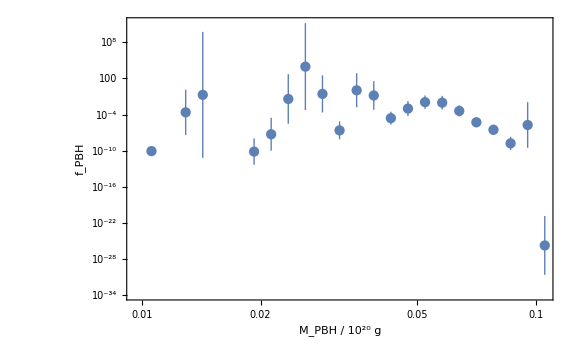

```mathematica
ListLogLogPlot[fPBHis,Joined->False,FrameLabel->{"M_PBH / 10^20 g",Subscript[f, PBH]}]
```